# Networks

"BipartiteEmbedding"
"CircularEmbedding"
"CircularMultipartiteEmbedding"
"DiscreteSpiralEmbedding"
"GridEmbedding"
"LinearEmbedding"
"MultipartiteEmbedding"
"SpiralEmbedding"
"StarEmbedding"

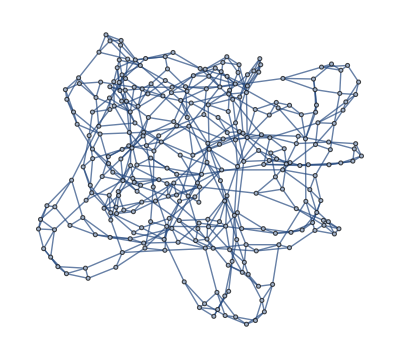

```mathematica
distribution=WattsStrogatzGraphDistribution[300,0.1];
graph=RandomGraph[distribution
,GraphLayout->"SpringElectricalEmbedding"
]
```

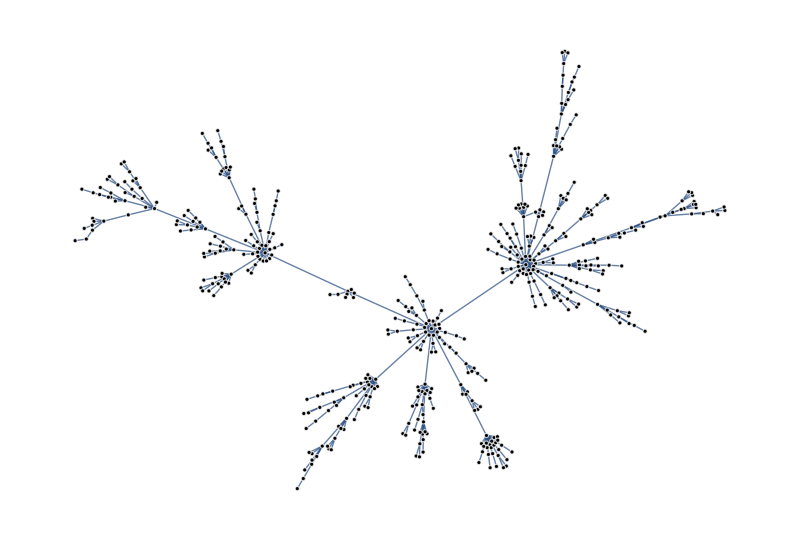

```mathematica
distribution=BarabasiAlbertGraphDistribution[500,1];
graph=RandomGraph[distribution
,GraphLayout->"SpringElectricalEmbedding"
,ImageSize->800
,VertexStyle->Directive[Black,EdgeForm[Directive[White,Thick]]]
]
```

```mathematica
CommunityGraphPlot[graph
,ImageSize->750
]
```

-Graphics-

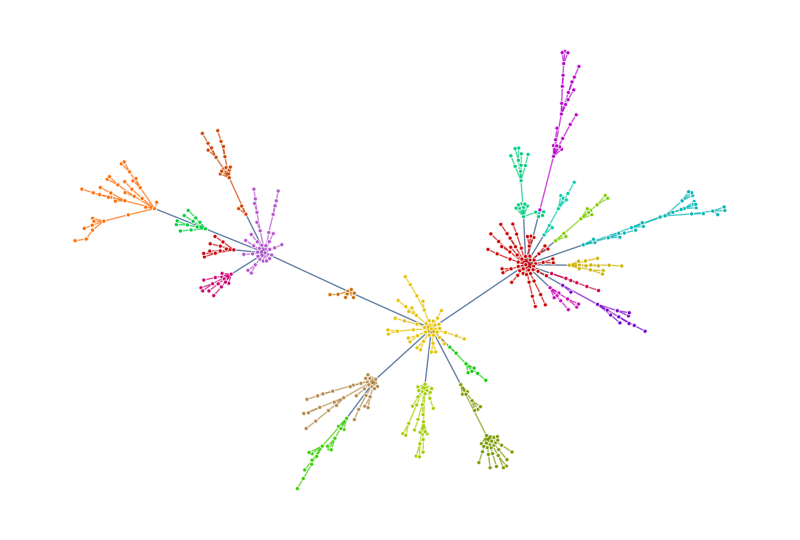

```mathematica
communities=FindGraphCommunities[graph,Method->"Centrality"];
HighlightGraph[graph,Map[Subgraph[graph,#]&, %]]
```

```mathematica
bet=BetweennessCentrality[graph];
HighlightGraph[graph,VertexList[graph],VertexSize-> Thread[VertexList[graph]-> 5*Rescale[%]]]
```

-Graphics-